```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
(**********************************************)
(*******Generate plot in Figure S5C****************) 
(**********************************************)
```

```mathematica
(**************RiboGCaMP data******************)
```

```mathematica
dateMouseSessionList={{"060323","Mouse493a","Session1"},{"060323","Mouse493a","Session2"},{"060323","Mouse493a","Session3"},{"060323","Mouse493b","Session1"},{"060323","Mouse493b","Session2"},{"060323","Mouse493b","Session1"},{"060323","Mouse493b","Session2"},{"060323","Mouse493b","Session1"}};
```

```mathematica
numROIsList=Table[Length[FileNames["*.txt",StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/NeuropilFs/"]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
neuropilFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/NeuropilFs/","fNP",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Neuropil fluorescence values*)
```

```mathematica
neuropildFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/NeuropildFs/","dfNP",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Neuropil dF values*)
```

```mathematica
cellbodyFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/CellBodyFs/","fCB",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Cell body fluorescence values*)
```

```mathematica
cellbodydFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/CellBodydFs/","dfCB",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Cell body dF values*)
```

```mathematica
riboGcbSDs=StandardDeviation/@cellbodyFs;(*Cell body fluorescence standard deviation*)
```

```mathematica
riboGnpSDs=StandardDeviation/@neuropilFs;(*Neuropil fluorescence standard deviation*)
```

```mathematica
cellBodydFsHists=Table[HistogramList[cellbodydFs[[n]],{0,200,1},"Probability"][[2]],{n,1,Length[cellbodydFs]}];(*List of cell body dF histograms*)
```

```mathematica
neuropildFsHists=Table[HistogramList[neuropildFs[[n]],{0,200,1},"Probability"][[2]],{n,1,Length[neuropildFs]}];(*List of neuropil dF histograms*)
```

```mathematica
cellBodyMedians=Median/@cellbodydFs;
```

```mathematica
neuropilMedians=Median/@neuropildFs;
```

```mathematica
roiListCBmedSort=Part[#,1]&/@Sort[Table[{n,cellBodyMedians[[n]]},{n,1,Length[cellbodydFs]}],#1[[2]]<#2[[2]]&];(*Sort by median dF*)
```

```mathematica
roiListNPmedSort=Part[#,1]&/@Sort[Table[{n,neuropilMedians[[n]]},{n,1,Length[neuropildFs]}],#1[[2]]<#2[[2]]&];(*Sort by median dF*)
```

```mathematica
cellBodyDFhistArray=Table[cellBodydFsHists[[n]],{n,roiListCBmedSort}];
```

```mathematica
neuropilDFhistArray=Table[neuropildFsHists[[n]],{n,roiListNPmedSort}];
```

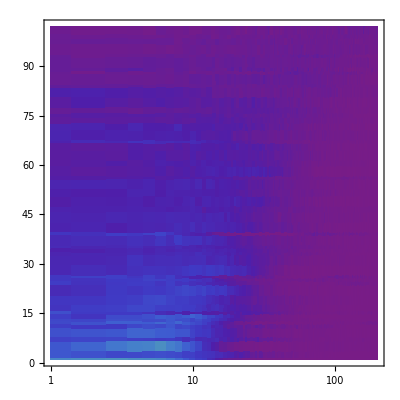

```mathematica
ListDensityPlot[cellBodyDFhistArray,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"]@Rescale[#,{0,0.3},{0,1}]&),PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}](*Cell body dF histogram density plot*)
```

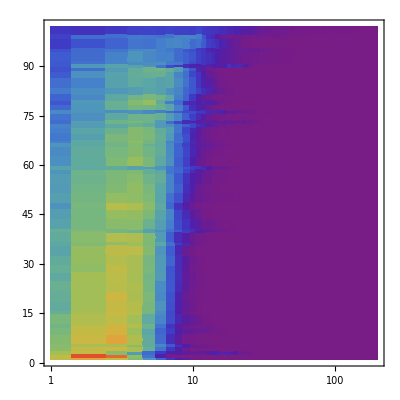

```mathematica
ListDensityPlot[neuropilDFhistArray,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"]@Rescale[#,{0,0.3},{0,1}]&),PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}](*Neuropil dF histogram density plot*)
```

```mathematica
(********************GCaMP6s data*************************)
```

```mathematica
dateMouseSessionList={{"021321","Mouse23359","Session1"},{"092620","Mouse21069","Session2"},{"093020","Mouse21069","Session2"},{"111420","Mouse23386","Session3"},{"111720","Mouse23386","Session3"}};
```

```mathematica
numROIsList=Table[Length[FileNames["*.txt",StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/NeuropilFs/"]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
neuropilFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/NeuropilFs/","fNP",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Neuropil fluorescence values*)
```

```mathematica
neuropildFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/NeuropildFs/","dfNP",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Neuropil dF values*)
```

```mathematica
cellbodyFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/CellBodyFs/","fCB",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Cell body fluorescence values*)
```

```mathematica
cellbodydFs=Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/ForG6sVsRiboG/CellBodydFs/","dfCB",ToString[roi],".txt"],"List"],{roi,1,numROIsList[[n]]}],{n,1,Length[dateMouseSessionList]}],1];(*Cell body dF values*)
```

```mathematica
g6ScbSDs=StandardDeviation/@cellbodyFs;(*Cell body fluorescence standard deviation*)
```

```mathematica
g6SnpSDs=StandardDeviation/@neuropilFs;(*Neuropil fluorescence standard deviation*)
```

```mathematica
cellBodydFsHists=Table[HistogramList[cellbodydFs[[n]],{0,200,1},"Probability"][[2]],{n,1,Length[cellbodydFs]}];(*List of cell body dF histograms*)
```

```mathematica
neuropildFsHists=Table[HistogramList[neuropildFs[[n]],{0,200,1},"Probability"][[2]],{n,1,Length[neuropildFs]}];(*List of neuropil dF histograms*)
```

```mathematica
cellBodyMedians=Median/@cellbodydFs;
```

```mathematica
neuropilMedians=Median/@neuropildFs;
```

```mathematica
roiListCBmedSort=Part[#,1]&/@Sort[Table[{n,cellBodyMedians[[n]]},{n,1,Length[cellbodydFs]}],#1[[2]]<#2[[2]]&];(*Sort by median dF*)
```

```mathematica
roiListNPmedSort=Part[#,1]&/@Sort[Table[{n,neuropilMedians[[n]]},{n,1,Length[neuropildFs]}],#1[[2]]<#2[[2]]&];(*Sort by median dF*)
```

```mathematica
cellBodyDFhistArray=Table[cellBodydFsHists[[n]],{n,roiListCBmedSort}];
```

```mathematica
neuropilDFhistArray=Table[neuropildFsHists[[n]],{n,roiListNPmedSort}];
```

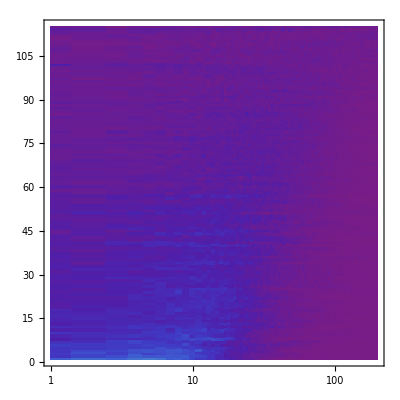

```mathematica
ListDensityPlot[cellBodyDFhistArray,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"]@Rescale[#,{0,0.3},{0,1}]&),PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}](*Cell body dF histogram density plot*)
```

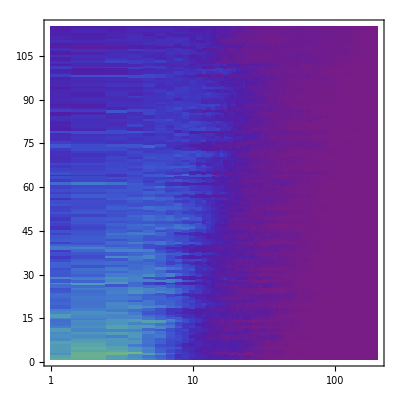

```mathematica
ListDensityPlot[neuropilDFhistArray,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"]@Rescale[#,{0,0.3},{0,1}]&),PlotRange->All,ScalingFunctions->{"Log","Linear","Linear"}](*Neuropil dF histogram density plot*)
```

```mathematica
(**********************************************)
(*******Generate plot in Figure S5D,E****************) 
(**********************************************)
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{g6ScbSDs,riboGcbSDs},"Log",hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Black,Darker@Green}),PerformanceGoal->"Speed",PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
h2=Histogram[{g6ScbSDs,riboGcbSDs},"Log",hfn,ChartStyle->{{Black,Darker@Green},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
g6Smedian=ListLogLinearPlot[{{Median[g6ScbSDs],0.5}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
riboGmedian=ListLogLinearPlot[{{Median[riboGcbSDs],0.5}},PlotStyle->Darker@Green,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
mark1=ListLogLinearPlot[{{1,0.48}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
mark5=ListLogLinearPlot[{{5,0.48}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
mark10=ListLogLinearPlot[{{10,0.48}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

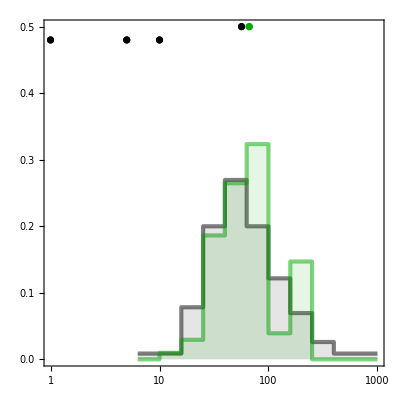

```mathematica
Show[hline,h2,g6Smedian,riboGmedian,mark1,mark5,mark10,AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{g6SnpSDs,riboGnpSDs},"Log",hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Gray,Green}),PerformanceGoal->"Speed",PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
h2=Histogram[{g6SnpSDs,riboGnpSDs},"Log",hfn,ChartStyle->{{Gray,Green},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
g6Smedian=ListLogLinearPlot[{{Median[g6SnpSDs],0.5}},PlotStyle->Gray,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
riboGmedian=ListLogLinearPlot[{{Median[riboGnpSDs],0.5}},PlotStyle->Green,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
mark1=ListLogLinearPlot[{{1,0.48}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
mark5=ListLogLinearPlot[{{5,0.48}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

```mathematica
mark10=ListLogLinearPlot[{{10,0.48}},PlotStyle->Black,PlotRange->{{0,250},{0,0.5}},FrameTicks->{{LinTicks[0,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,250,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick];
```

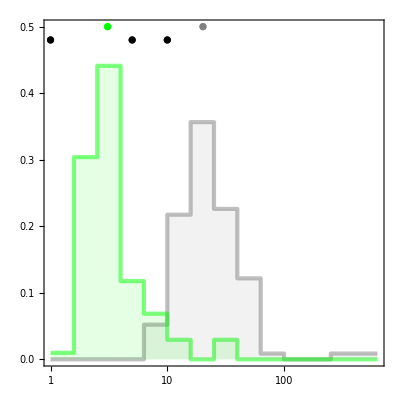

```mathematica
Show[hline,h2,g6Smedian,riboGmedian,mark1,mark5,mark10,AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```